```mathematica
(*definizioni mie*)
rapp[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]/x2[[i,2]]},{i,1,Length[x1]}]
absrapp[x1_,x2_]:=Table[{x1[[i,1]],Abs[x1[[i,2]]/x2[[i,2]]]},{i,1,Length[x1]}]
mult[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]*x2[[i,2]]},{i,1,Length[x1]}]
sum[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]+x2[[i,2]]},{i,1,Length[x1]}]
sumlist[x1_]:=Table[{x1[[1,i,1]],x1[[1,i,2]]+x1[[2,i,2]]+x1[[3,i,2]]},{i,1,Length[x1[[1]]]}]
coeff[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]*c},{i,1,Length[x1]}]
sumconst[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]+c},{i,1,Length[x1]}]
diff[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]-x2[[i,2]]},{i,1,Length[x1]}]
joinbin[x_,n_]:=Map[{(Plus@@#)[[1]]/n,(Plus@@#)[[2]]}&,Partition[x,n]]

(* FORSE MANCANO DEI MEZZI sommando sulle polarizzazioni?  NO!*)
```

```mathematica
μPDFpart[WmT,Q_]=(μPDFpart[Wmp,Q][#]+ μPDFpart[Wmm,Q][#])/1&
μPDFpart[WpT,Q_]=(μPDFpart[Wpp,Q][#]+ μPDFpart[Wpm,Q][#])/1&
μPDFpart[ZT,Q_]=(μPDFpart[Zp,Q][#]+ μPDFpart[Zm,Q][#])/1&
μPDFpart[γ,Q_]=(μPDFpart[γp,Q][#]+ μPDFpart[γm,Q][#])/1&

μbPDFpart[WmT,Q_]=(μbPDFpart[Wmp,Q][#]+ μbPDFpart[Wmm,Q][#])/1&
μbPDFpart[WpT,Q_]=(μbPDFpart[Wpp,Q][#]+ μbPDFpart[Wpm,Q][#])/1&
μbPDFpart[ZT,Q_]=(μbPDFpart[Zp,Q][#]+ μbPDFpart[Zm,Q][#])/1&
μbPDFpart[γ,Q_]=(μbPDFpart[γp,Q][#]+ μbPDFpart[γm,Q][#])/1&
```

(μPDFpart[Wmp,Q][#1]+μPDFpart[Wmm,Q][#1]) 1/1&

(μPDFpart[Wpp,Q][#1]+μPDFpart[Wpm,Q][#1]) 1/1&

(μPDFpart[Zp,Q][#1]+μPDFpart[Zm,Q][#1]) 1/1&

(μPDFpart[γp,Q][#1]+μPDFpart[γm,Q][#1]) 1/1&

(μbPDFpart[Wmp,Q][#1]+μbPDFpart[Wmm,Q][#1]) 1/1&

(μbPDFpart[Wpp,Q][#1]+μbPDFpart[Wpm,Q][#1]) 1/1&

(μbPDFpart[Zp,Q][#1]+μbPDFpart[Zm,Q][#1]) 1/1&

(μbPDFpart[γp,Q][#1]+μbPDFpart[γm,Q][#1]) 1/1&

```mathematica
energieQplot={1TeV, 3TeV, 10 TeV, 30 TeV};
Do[
Qplot = energieQplot[[i]];
(* LA SCALA É STOT DEL COLLIDER*)
plotmio = LogLogPlot[{
μPDFpart[μL,Qplot][x]+μPDFpart[μR,Qplot][x],
μPDFpart[γp,Qplot][x]+ μPDFpart[γm,Qplot][x],
(*μPDFpart[gp,Qplot][x]+ μPDFpart[gm,Qplot][x],*)
μPDFpart[Wmp,Qplot][x]+ μPDFpart[Wmm,Qplot][x],μPDFpart[WmL,Qplot][x],
μPDFpart[Wpp,Qplot][x]+ μPDFpart[Wpm,Qplot][x],μPDFpart[WpL,Qplot][x],
μPDFpart[Zp,Qplot][x]+ μPDFpart[Zm,Qplot][x], μPDFpart[ZL,Qplot][x]
(*μPDFpart[νμ,Qplot][x],
 μPDFpart[νeb,Qplot][x],*)
(*μPDFpart[eL,Qplot][x]+μPDFpart[eR,Qplot][x]
qPDF[x] *)
},{x,10^-4,0.9909},PlotStyle->{Black,Orange,Brown,Red,Darker[Green],Cyan,Gray,Purple,Blue,Magenta},PlotRange->{{0.00099,1},{0.001,100}},Frame->True,FrameLabel->{"x","f_i(x,Q)"},RotateLabel->True,BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550,PlotLegends->{"mu","γ","W-_T","W-_L","W+_T","W+_L","Z_T","Z_L"},PlotLabel->"PDFs of μ-, Q = "<>ToString[Qplot/1000]<>" TeV"];

plotmiomuplus = LogLogPlot[{
μbPDFpart[μL,Qplot][x]+μbPDFpart[μR,Qplot][x],
μbPDFpart[γp,Qplot][x]+ μbPDFpart[γm,Qplot][x],
(*μbPDFpart[gp,Qplot][x]+ μbPDFpart[gm,Qplot][x],*)
μbPDFpart[Wmp,Qplot][x]+ μbPDFpart[Wmm,Qplot][x],μbPDFpart[WmL,Qplot][x],
μbPDFpart[Wpp,Qplot][x]+ μbPDFpart[Wpm,Qplot][x],μbPDFpart[WpL,Qplot][x],
μbPDFpart[Zp,Qplot][x]+ μbPDFpart[Zm,Qplot][x], μbPDFpart[ZL,Qplot][x]
(*μbPDFpart[νμ,Qplot][x],
 μbPDFpart[νeb,Qplot][x],*)
(*μbPDFpart[eL,Qplot][x]+μbPDFpart[eR,Qplot][x]
qPDF[x] *)
},{x,10^-4,0.9909},PlotStyle->{Black,Orange,Brown,Red,Darker[Green],Cyan,Gray,Purple,Blue,Magenta},PlotRange->{{0.00099,1},{0.001,100}},Frame->True,FrameLabel->{"x","f_i(x,Q)"},RotateLabel->True,BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550,PlotLegends->{"mu","γ","W-_T","W-_L","W+_T","W+_L","Z_T","Z_L"},PlotLabel->"PDFs of μ+, Q = "<>ToString[Qplot/1000]<>" TeV"];

(* LA SCALA É STOT DEL COLLIDER PER SQRT[X]*)
plotmiov3 = LogLogPlot[{
μPDFpart[μL,Qplot Sqrt[x]][x]+μPDFpart[μR,Qplot Sqrt[x]][x],
μPDFpart[γp,Qplot Sqrt[x]][x]+ μPDFpart[γm,Qplot Sqrt[x]][x],
(*μPDFpart[gp,Qplot Sqrt[x]][x]+ μPDFpart[gm,Qplot Sqrt[x]][x],*)
μPDFpart[Wmp,Qplot Sqrt[x]][x]+ μPDFpart[Wmm,Qplot Sqrt[x]][x],μPDFpart[WmL,Qplot Sqrt[x]][x],
μPDFpart[Wpp,Qplot Sqrt[x]][x]+ μPDFpart[Wpm,Qplot Sqrt[x]][x],μPDFpart[WpL,Qplot Sqrt[x]][x],
μPDFpart[Zp,Qplot Sqrt[x]][x]+ μPDFpart[Zm,Qplot Sqrt[x]][x], μPDFpart[ZL,Qplot Sqrt[x]][x]
(*μPDFpart[νμ,Qplot Sqrt[x]][x],
 μPDFpart[νeb,Qplot Sqrt[x]][x],*)
(*μPDFpart[eL,Qplot Sqrt[x]][x]+μPDFpart[eR,Qplot Sqrt[x]][x]
qPDF[x]*) 
},{x,10^-4,0.9909},PlotStyle->{Black,Orange,Brown,Red,Darker[Green],Cyan,Gray,Purple,Blue,Magenta},PlotRange->{{0.00099,1},{0.001,100}},Frame->True,FrameLabel->{"x","f_i(x,Q)"},RotateLabel->True,BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550,PlotLegends->{"mu","γ","W-_T","W-_L","W+_T","W+_L","Z_T","Z_L"},PlotLabel->"PDFs of μ-, Q = Sqrt[x] "<>ToString[Qplot/1000]<>" TeV"];

plotmiomuplusv3 = LogLogPlot[{
μbPDFpart[μL,Qplot Sqrt[x]][x]+μbPDFpart[μR,Qplot Sqrt[x]][x],
μbPDFpart[γp,Qplot Sqrt[x]][x]+ μbPDFpart[γm,Qplot Sqrt[x]][x],
(*μbPDFpart[gp,Qplot Sqrt[x]][x]+ μbPDFpart[gm,Qplot Sqrt[x]][x],*)
μbPDFpart[Wmp,Qplot Sqrt[x]][x]+ μbPDFpart[Wmm,Qplot Sqrt[x]][x],μbPDFpart[WmL,Qplot Sqrt[x]][x],
μbPDFpart[Wpp,Qplot Sqrt[x]][x]+ μbPDFpart[Wpm,Qplot Sqrt[x]][x],μbPDFpart[WpL,Qplot Sqrt[x]][x],
μbPDFpart[Zp,Qplot Sqrt[x]][x]+ μbPDFpart[Zm,Qplot Sqrt[x]][x], μbPDFpart[ZL,Qplot Sqrt[x]][x]
(*μbPDFpart[νμ,Qplot Sqrt[x]][x],
 μbPDFpart[νeb,Qplot Sqrt[x]][x],*)
(*μbPDFpart[eL,Qplot Sqrt[x]][x]+μbPDFpart[eR,Qplot Sqrt[x]][x]
qPDF[x]*) 
},{x,10^-4,0.9909},PlotStyle->{Black,Orange,Brown,Red,Darker[Green],Cyan,Gray,Purple,Blue,Magenta},PlotRange->{{0.00099,1},{0.001,100}},Frame->True,FrameLabel->{"x","f_i(x,Q)"},RotateLabel->True,BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550,PlotLegends->{"mu","γ","W-_T","W-_L","W+_T","W+_L","Z_T","Z_L"},PlotLabel->"PDFs of μ+, Q = Sqrt[x] "<>ToString[Qplot/1000]<>" TeV"];


(* LA SCALA É STOT DEL COLLIDER PER [X]*)
plotmiov2 = LogLogPlot[{
μPDFpart[μL,Qplot x][x]+μPDFpart[μR,Qplot x][x],
μPDFpart[γp,Qplot x][x]+ μPDFpart[γm,Qplot x][x],
(*μPDFpart[gp,Qplot x][x]+ μPDFpart[gm,Qplot x][x],*)
μPDFpart[Wmp,Qplot x][x]+ μPDFpart[Wmm,Qplot x][x],μPDFpart[WmL,Qplot x][x],
μPDFpart[Wpp,Qplot x][x]+ μPDFpart[Wpm,Qplot x][x],μPDFpart[WpL,Qplot x][x],
μPDFpart[Zp,Qplot x][x]+ μPDFpart[Zm,Qplot x][x], μPDFpart[ZL,Qplot x][x]
(*μPDFpart[νμ,Qplot x][x],
 μPDFpart[νeb,Qplot x][x],*)
(*μPDFpart[eL,Qplot x][x]+μPDFpart[eR,Qplot x][x]
qPDF[x]*) 
},{x,10^-4,0.9909},PlotStyle->{Black,Orange,Brown,Red,Darker[Green],Cyan,Gray,Purple,Blue,Magenta},PlotRange->{{0.00099,1},{0.001,100}},Frame->True,FrameLabel->{"x","f_i(x,Q)"},RotateLabel->True,BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550,PlotLegends->{"mu","γ","W-_T","W-_L","W+_T","W+_L","Z_T","Z_L"},PlotLabel->"PDFs of μ-, Q = x "<>ToString[Qplot/1000]<>" TeV"];

plotmiomuplusv2 = LogLogPlot[{
μbPDFpart[μL,Qplot x][x]+μbPDFpart[μR,Qplot x][x],
μbPDFpart[γp,Qplot x][x]+ μbPDFpart[γm,Qplot x][x],
(*μbPDFpart[gp,Qplot x][x]+ μbPDFpart[gm,Qplot x][x],*)
μbPDFpart[Wmp,Qplot x][x]+ μbPDFpart[Wmm,Qplot x][x],μbPDFpart[WmL,Qplot x][x],
μbPDFpart[Wpp,Qplot x][x]+ μbPDFpart[Wpm,Qplot x][x],μbPDFpart[WpL,Qplot x][x],
μbPDFpart[Zp,Qplot x][x]+ μbPDFpart[Zm,Qplot x][x], μbPDFpart[ZL,Qplot x][x]
(*μbPDFpart[νμ,Qplot x][x],
 μbPDFpart[νeb,Qplot x][x],*)
(*μbPDFpart[eL,Qplot x][x]+μbPDFpart[eR,Qplot x][x]
qPDF[x]*) 
},{x,10^-4,0.9909},PlotStyle->{Black,Orange,Brown,Red,Darker[Green],Cyan,Gray,Purple,Blue,Magenta},PlotRange->{{0.00099,1},{0.001,100}},Frame->True,FrameLabel->{"x","f_i(x,Q)"},RotateLabel->True,BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550,PlotLegends->{"mu","γ","W-_T","W-_L","W+_T","W+_L","Z_T","Z_L"},PlotLabel->"PDFs of μ+, Q = x "<>ToString[Qplot/1000]<>" TeV"];

Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotPDFs/alltogether/"<>ToString[Qplot/1000]<>"TeV_mu-scaleQ.pdf",plotmio ];
Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotPDFs/alltogether/"<>ToString[Qplot/1000]<>"TeV_mu+scaleQ.pdf",plotmiomuplus ];
Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotPDFs/alltogether/"<>ToString[Qplot/1000]<>"TeV_mu-scaleQx.pdf",plotmiov2 ];
Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotPDFs/alltogether/"<>ToString[Qplot/1000]<>"TeV_mu+scaleQx.pdf",plotmiomuplusv2 ];
Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotPDFs/alltogether/"<>ToString[Qplot/1000]<>"TeV_mu-scaleQsqrtx.pdf",plotmiov3 ];
Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotPDFs/alltogether/"<>ToString[Qplot/1000]<>"TeV_mu+scaleQsqrtx.pdf",plotmiomuplusv3 ]



,{i,1,Length[energieQplot]}]
```

InterpolatingFunction::dmval: Input value {-0.109706} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.49546} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
(*valore usato nei primi test alpha=1/137.*)
(*alpha in realtà runna nelle PDF!!!!!*)
alpha= 0.00783581(*Initial condition in LePDF at MW*)
e=Sqrt[4Pi alpha]
MZ=91.1876
MW=80.379(* come nei run di MG5 e non 80.379*)
cw=Sqrt[MW^2/MZ^2]
sw=Sqrt[1-cw^2]
g=e/sw
```

0.00783581

0.313796

91.1876

80.379

0.881469

0.472243

0.664479

```mathematica
(*gV=.
gL=.
gR=.
gt=.
MV=.*)
```

```mathematica
rulesW={(*gV->1/2*)gV->1,gL->1,gR->0,gt->g/Sqrt[2],MV->MW}

μLEVApart[Wmp,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 (1-x)^2/(2x)Log[Q^2/MV^2] /.rulesW(*2.7 a*)
μLEVApart[Wmm,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 /(2x)Log[Q^2/MV^2]/.rulesW (*2.7 b*)
μLEVApart[WmL,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 (1-x)/(x)/.rulesW(*2.7 c*)

μREVApart[Wmp,Q_,x_]:=(gR^2/gL^2) μLEVApart[Wmm,Q,x] /.rulesW(*2.7 d*)
μREVApart[Wmm,Q_,x_]:=(gR^2/gL^2) μLEVApart[Wmp,Q,x] /.rulesW(*2.7 e*)
μREVApart[WmL,Q_,x_]:=(gR^2/gL^2) μLEVApart[WmL,Q,x] /.rulesW(*2.7 f*)


μEVApart[Wmp,Q_,x_]:=(μLEVApart[Wmp,Q,x]+μREVApart[Wmp,Q,x])/2
μEVApart[Wmm,Q_,x_]:=(μLEVApart[Wmm,Q,x]+μREVApart[Wmm,Q,x])/2
μEVApart[WmL,Q_,x_]:=(μLEVApart[WmL,Q,x]+μREVApart[WmL,Q,x])/2


(*Scale as LEPDF EVA*)

μLEVApartv2[Wmp,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 (1-x)^2/(2x)(Log[(Q^2+(1-x)MV^2)/(MV^2*(1-x))]-Q^2/(Q^2+(1-x)MV^2))  /.rulesW(*2.7 a*)
μLEVApartv2[Wmm,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 /(2x)(Log[(Q^2+(1-x)MV^2)/(MV^2*(1-x))]-Q^2/(Q^2+(1-x)MV^2)) /.rulesW (*2.7 b*)
μLEVApartv2[WmL,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 (1-x)/(x)/.rulesW(*2.7 c*)

μREVApartv2[Wmp,Q_,x_]:=(gR^2/gL^2) μLEVApartv2[Wmm,Q,x] /.rulesW(*2.7 d*)
μREVApartv2[Wmm,Q_,x_]:=(gR^2/gL^2) μLEVApartv2[Wmp,Q,x] /.rulesW(*2.7 e*)
μREVApartv2[WmL,Q_,x_]:=(gR^2/gL^2) μLEVApartv2[WmL,Q,x] /.rulesW(*2.7 f*)


μEVApartv2[Wmp,Q_,x_]:=(μLEVApartv2[Wmp,Q,x]+μREVApartv2[Wmp,Q,x])/2
μEVApartv2[Wmm,Q_,x_]:=(μLEVApartv2[Wmm,Q,x]+μREVApartv2[Wmm,Q,x])/2
μEVApartv2[WmL,Q_,x_]:=(μLEVApartv2[WmL,Q,x]+μREVApartv2[WmL,Q,x])/2
```

{gV→1,gL→1,gR→0,gt→0.469858,MV→80.379}

```mathematica
(*

EVA RICHARD:


 Log[Q^2/MV^2]

*)


(*

EVA DAVID:


 (Log[(Q^2+(1-x)MV^2)/(MV^2*(1-x))]-Q^2/(Q^2+(1-x)MV^2))  

*)
```

10000

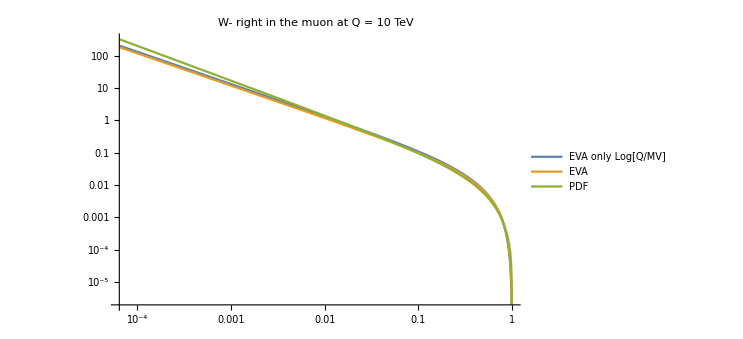

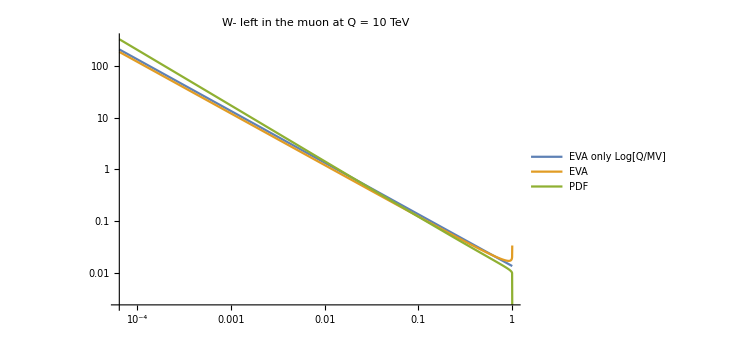

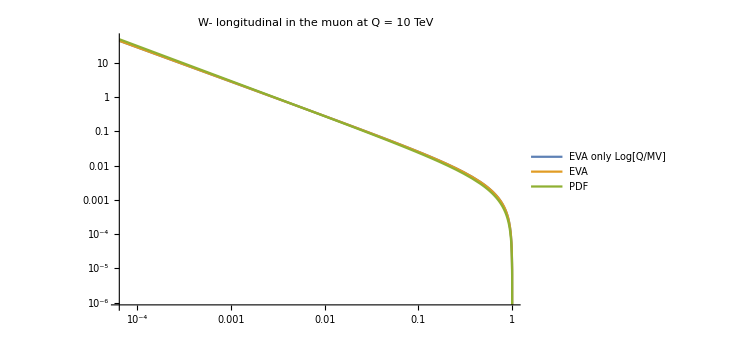

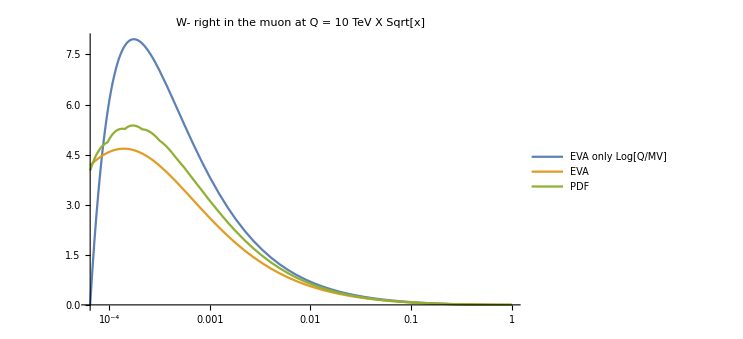

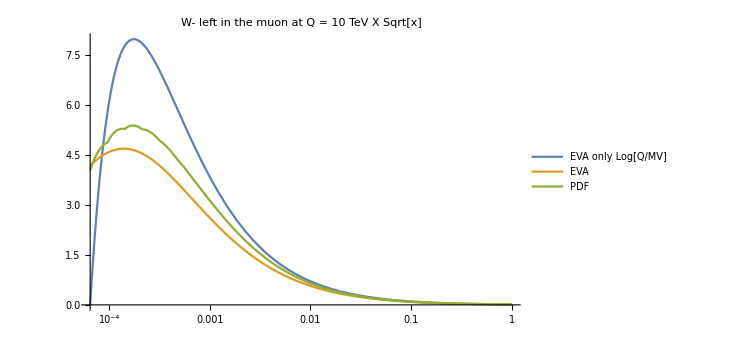

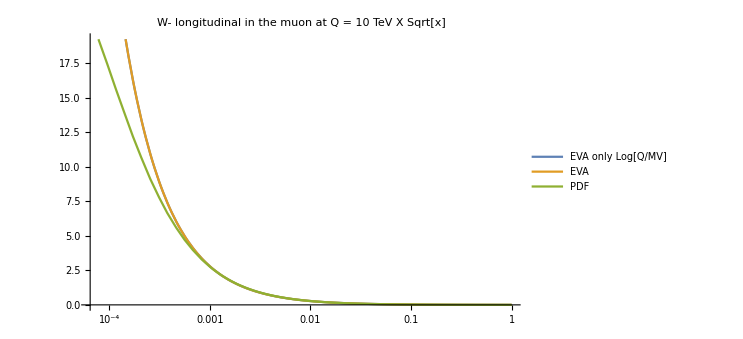

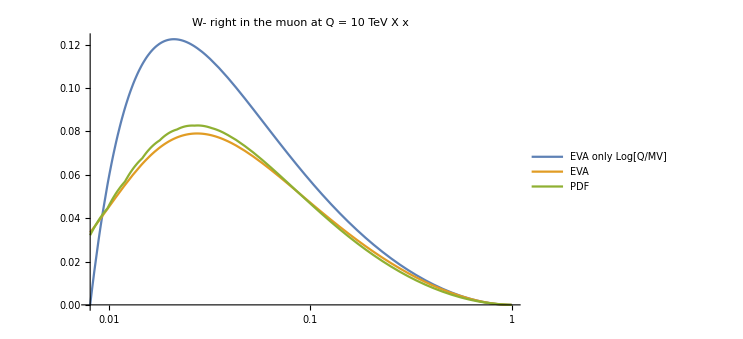

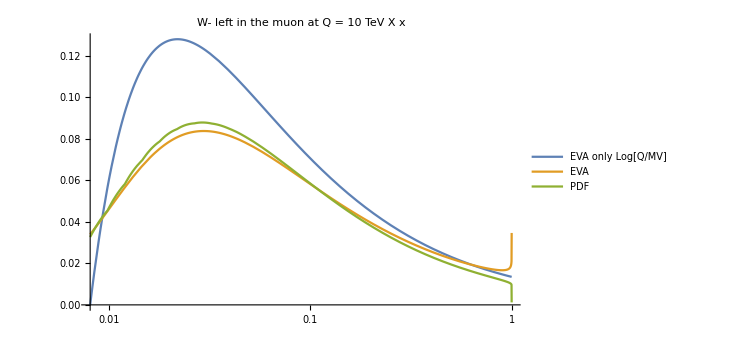

```mathematica
Q=10000


LogLogPlot[{μEVApart[Wmp,Q ,x],μEVApartv2[Wmp,Q ,x],μPDFpart[Wmp,Q][x]},{x,(MW/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"W- right in the muon at Q = "<>ToString[Q/1000]<>" TeV",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]
LogLogPlot[{μEVApart[Wmm,Q ,x],μEVApartv2[Wmm,Q ,x],μPDFpart[Wmm,Q][x]},{x,(MW/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"W- left in the muon at Q = "<>ToString[Q/1000]<>" TeV",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]
LogLogPlot[{μEVApart[WmL,Q ,x],μEVApartv2[WmL,Q ,x],μPDFpart[WmL,Q][x]},{x,(MW/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"W- longitudinal in the muon at Q = "<>ToString[Q/1000]<>" TeV",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]

LogLinearPlot[{μEVApart[Wmp,Q Sqrt[x],x],μEVApartv2[Wmp,Q Sqrt[x],x],μPDFpart[Wmp,Q Sqrt[x]][x]},{x,(MW/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"W- right in the muon at Q = "<>ToString[Q/1000]<>" TeV X Sqrt[x]",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]
LogLinearPlot[{μEVApart[Wmm,Q Sqrt[x],x],μEVApartv2[Wmm,Q Sqrt[x],x],μPDFpart[Wmm,Q Sqrt[x]][x]},{x,(MW/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"W- left in the muon at Q = "<>ToString[Q/1000]<>" TeV X Sqrt[x]",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]
LogLinearPlot[{μEVApart[WmL,Q Sqrt[x],x],μEVApartv2[WmL,Q Sqrt[x],x],μPDFpart[WmL,Q Sqrt[x]][x]},{x,(MW/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"W- longitudinal in the muon at Q = "<>ToString[Q/1000]<>" TeV X Sqrt[x]",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]


LogLinearPlot[{μEVApart[Wmp,Q x,x],μEVApartv2[Wmp,Q x,x],μPDFpart[Wmp,Q x][x]},{x,(MW/Q)^1,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"W- right in the muon at Q = "<>ToString[Q/1000]<>" TeV X x",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]
LogLinearPlot[{μEVApart[Wmm,Q x,x],μEVApartv2[Wmm,Q x,x],μPDFpart[Wmm,Q x][x]},{x,(MW/Q)^1,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"W- left in the muon at Q = "<>ToString[Q/1000]<>" TeV X x",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]
LogLinearPlot[{μEVApart[WmL,Q x,x],μEVApartv2[WmL,Q x,x],μPDFpart[WmL,Q x][x]},{x,(MW/Q)^1,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"W- longitudinal in the muon at Q = "<>ToString[Q/1000]<>" TeV X x",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]
```

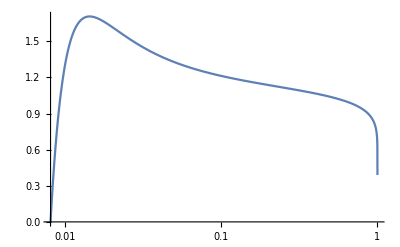

```mathematica
LogLinearPlot[{μEVApart[Wmp,Q x ,x]/μEVApartv2[Wmp,Q x,x]},{x,(MW/Q),1}]
```

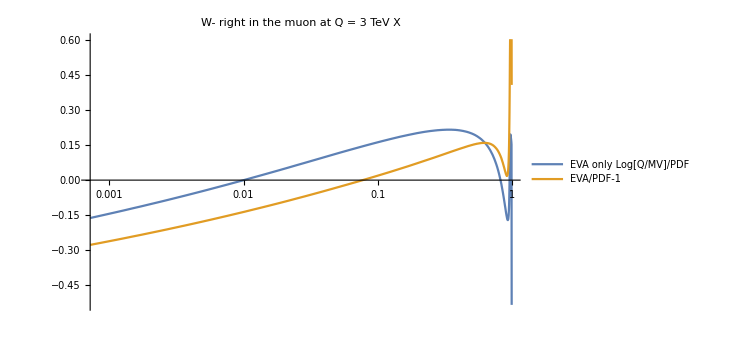

```mathematica
LogLinearPlot[{μEVApart[Wmp,Q ,x]/μPDFpart[Wmp,Q ][x]-1,μEVApartv2[Wmp,Q ,x]/μPDFpart[Wmp,Q ][x]-1},{x,(MW/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]/PDF-1","EVA/PDF-1"},PlotLabel->"W- right in the muon at Q = "<>ToString[Q/1000]<>" TeV X ",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]
```

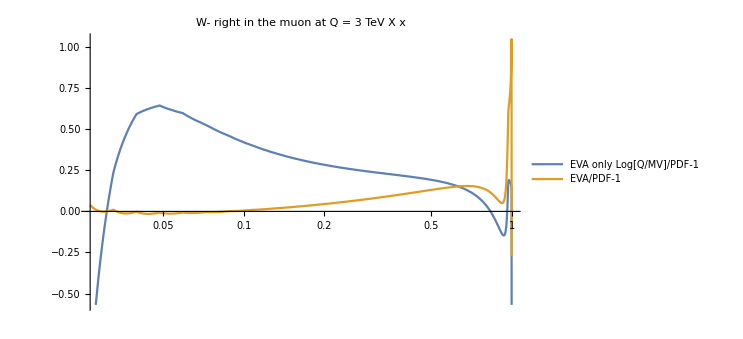

```mathematica
LogLinearPlot[{μEVApart[Wmp,Q x,x]/μPDFpart[Wmp,Q x][x]-1,μEVApartv2[Wmp,Q x,x]/μPDFpart[Wmp,Q x][x]-1},{x,(MW/Q)^1,1},PlotLegends->{"EVA only Log[Q/MV]/PDF-1","EVA/PDF-1"},PlotLabel->"W- right in the muon at Q = "<>ToString[Q/1000]<>" TeV X x",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]
```

```mathematica
(*μLEVApartv2[Wmp,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 (1-x)^2/(2x)(Log[(Q^2+(1-x)MV^2)/(MV^2*(1-x))]-Q^2/(Q^2+(1-x)MV^2)) /.rulesW(*2.7 a*)*)
```

```mathematica
LogLogPlot[{μLEVApart[Wmp,Q ,x],μLEVApart[Wmp,Q ,x]/2,μLEVApartv2[Wmp,Q,x],μLEVApartv2[Wmp,Q,x]/2,μPDFpart[Wmp,Q][x]},{x,0.001,1},PlotLegends->{"EVA only Log[Q/MV] μL ","EVA only Log[Q/MV]/2 μL ","EVA only Log[Q/MV] μL scale as David","EVA only Log[Q/MV]/2 μL scale as David ","PDF for μ not μL"},PlotLabel->"W- right in the muon"]
LogLinearPlot[{μLEVApart[Wmp,Q ,x]/μPDFpart[Wmp,Q][x]-1,μLEVApart[Wmp,Q ,x]/2/μPDFpart[Wmp,Q][x]-1,μLEVApartv2[Wmp,Q,x]/μPDFpart[Wmp,Q][x]-1,μLEVApartv2[Wmp,Q,x]/2/μPDFpart[Wmp,Q][x]-1,μPDFpart[Wmp,Q][x]/μPDFpart[Wmp,Q][x]-1},{x,0.001,0.5},PlotLegends->{"EVA only Log[Q/MV] μL ","EVA only Log[Q/MV]/2 μL ","EVA only Log[Q/MV] μL scale as David","EVA only Log[Q/MV]/2 μL scale as David ","PDF for μ not μL"},PlotLabel->"W- right in the muon: ratio with PDF for μ not μL"]

(*LogLogPlot[{ μEVApart[Wmp,Q ,x],μPDFpart[Wmp,Q][x]},{x,0.001,0.5}]
LogLinearPlot[{ μEVApart[Wmp,Q ,x]/μPDFpart[Wmp,Q][x]-1},{x,0.001,0.5}]
LogLinearPlot[{ (μEVApart[Wmp,Sqrt[Q ^2+MW^2(1-x)]/Sqrt[(1-x) /Exp[Q^2/(Q^2+(1-x)MW^2)]],x])/μPDFpart[Wmp,Q][x]-1},{x,0.001,0.5}]
LogLinearPlot[{μEVApart[Wmm,Q ,x]/μPDFpart[Wmm,Q][x]-1},{x,0.001,0.5}]
LogLinearPlot[{(μEVApart[Wmp,Q ,x]+μEVApart[Wmm,Q ,x])/μPDFpart[WmT,Q][x]-1},{x,0.001,0.5}]
LogLinearPlot[{μEVApart[WmL,Q ,x]/μPDFpart[WmL,Q][x]-1},{x,0.001,0.5}]*)
```

```mathematica
(*Plot di Debug*)
```

```mathematica
(-1/2)-(-1)*sw^2
```

-0.276987

```mathematica
(*!!!!!!!  !!!!!!!!*)
```

```mathematica
rulesZfL={(*gV->1/2*(-1/2)-(-1)sw^2,*)gV->1,gL->(-1/2)-(-1)sw^2,gR->-(-1)sw^2,gt->g/cw,MV->MZ}
rulesZfR={(*gV->1/2*(0)-(-1)sw^2,*)gV->1,gL->(0)-(-1)sw^2,gR->-(-1)sw^2,gt->g/cw,MV->MZ}

μLEVApart[Zp,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 (1-x)^2/(2x)Log[Q^2/MV^2] /.rulesZfL(*2.7 a*)
μLEVApart[Zm,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 /(2x)Log[Q^2/MV^2]/.rulesZfL (*2.7 b*)
μLEVApart[ZL,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 (1-x)/(x)/.rulesZfL(*2.7 c*)

μREVApart[Zp,Q_,x_]:=(gR^2/gL^2)gt^2gV^2/4/Pi^2gL^2 /(2x)Log[Q^2/MV^2] /.rulesZfR(*2.7 d*)
μREVApart[Zm,Q_,x_]:=(gR^2/gL^2) gt^2gV^2/4/Pi^2gL^2 (1-x)^2/(2x)Log[Q^2/MV^2] /.rulesZfR(*2.7 e*)
μREVApart[ZL,Q_,x_]:=(gR^2/gL^2)gt^2gV^2/4/Pi^2gL^2 (1-x)/(x) /.rulesZfR(*2.7 f*)

μEVApart[Zp,Q_,x_]:=(μLEVApart[Zp,Q,x]+μREVApart[Zp,Q,x])/2




μEVApart[Zm,Q_,x_]:=(μLEVApart[Zm,Q,x]+μREVApart[Zm,Q,x])/2



μEVApart[ZL,Q_,x_]:=(μLEVApart[ZL,Q,x]+μREVApart[ZL,Q,x])/2



(*Scale as LEPDF EVA*)

rulesZfL={(*gV->1/2*(-1/2)-(-1)sw^2,*)gV->1,gL->(-1/2)-(-1)sw^2,gR->-(-1)sw^2,gt->g/cw,MV->MZ}
rulesZfR={(*gV->1/2*(0)-(-1)sw^2,*)gV->1,gL->(0)-(-1)sw^2,gR->-(-1)sw^2,gt->g/cw,MV->MZ}

μLEVApartv2[Zp,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 (1-x)^2/(2x)(Log[(Q^2+(1-x)MV^2)/(MV^2*(1-x))]-Q^2/(Q^2+(1-x)MV^2))  /.rulesZfL(*2.7 a*)
μLEVApartv2[Zm,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 /(2x)(Log[(Q^2+(1-x)MV^2)/(MV^2*(1-x))]-Q^2/(Q^2+(1-x)MV^2)) /.rulesZfL (*2.7 b*)
μLEVApartv2[ZL,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 (1-x)/(x)/.rulesZfL(*2.7 c*)

μREVApartv2[Zp,Q_,x_]:=(gR^2/gL^2)gt^2gV^2/4/Pi^2gL^2 /(2x)(Log[(Q^2+(1-x)MV^2)/(MV^2*(1-x))]-Q^2/(Q^2+(1-x)MV^2))  /.rulesZfR(*2.7 d*)
μREVApartv2[Zm,Q_,x_]:=(gR^2/gL^2) gt^2gV^2/4/Pi^2gL^2 (1-x)^2/(2x)(Log[(Q^2+(1-x)MV^2)/(MV^2*(1-x))]-Q^2/(Q^2+(1-x)MV^2))  /.rulesZfR(*2.7 e*)
μREVApartv2[ZL,Q_,x_]:=(gR^2/gL^2)gt^2gV^2/4/Pi^2gL^2 (1-x)/(x) /.rulesZfR(*2.7 f*)

μEVApartv2[Zp,Q_,x_]:=(μLEVApartv2[Zp,Q,x]+μREVApartv2[Zp,Q,x])/2




μEVApartv2[Zm,Q_,x_]:=(μLEVApartv2[Zm,Q,x]+μREVApartv2[Zm,Q,x])/2



μEVApartv2[ZL,Q_,x_]:=(μLEVApartv2[ZL,Q,x]+μREVApartv2[ZL,Q,x])/2






μEVApart[Zp,Q,x]
```

{gV→1,gL→-0.276987,gR→0.223013,gt→0.753832,MV→91.1876}

{gV→1,gL→0.223013,gR→0.223013,gt→0.753832,MV→91.1876}

{gV→1,gL→-0.276987,gR→0.223013,gt→0.753832,MV→91.1876}

{gV→1,gL→0.223013,gR→0.223013,gt→0.753832,MV→91.1876}

1/2 (0.00336287/x+(0.00518761 (1-x)^2)/x)

3000

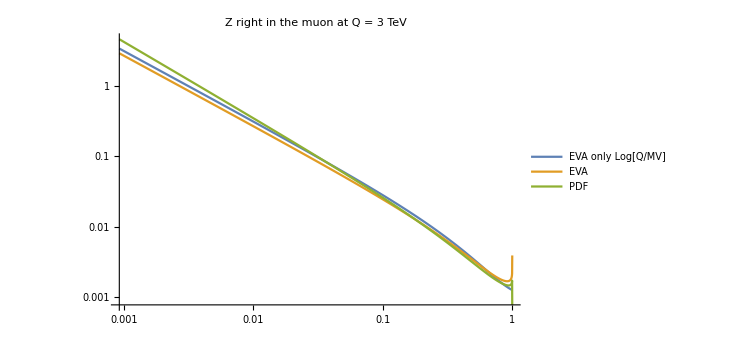

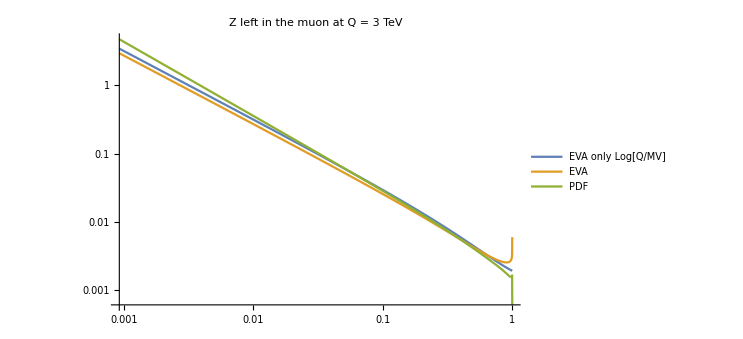

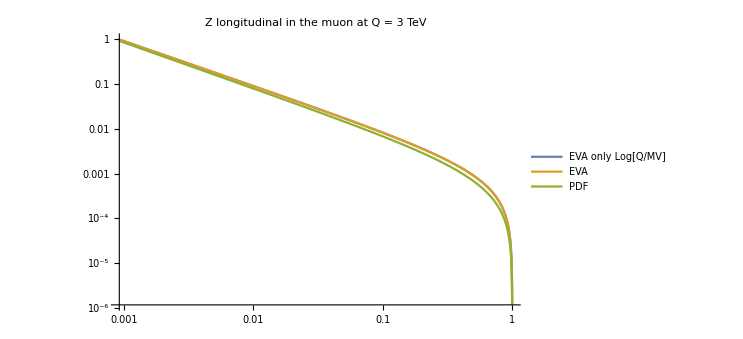

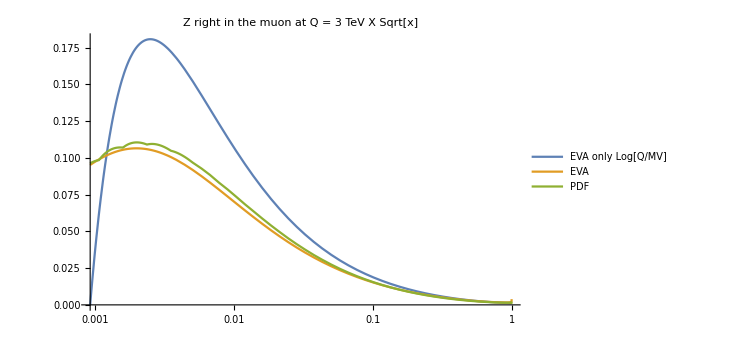

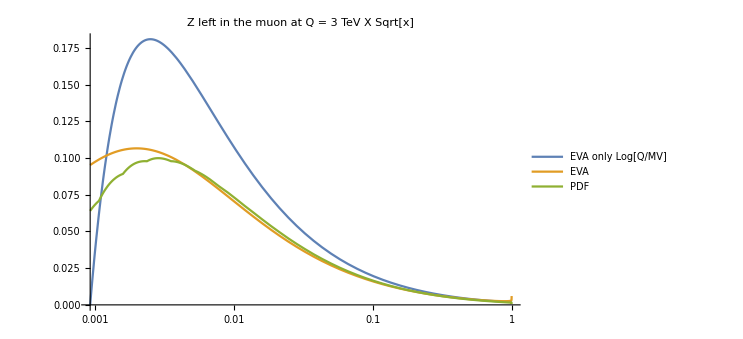

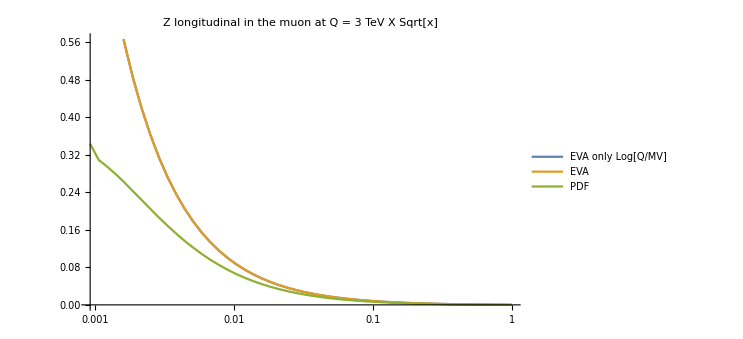

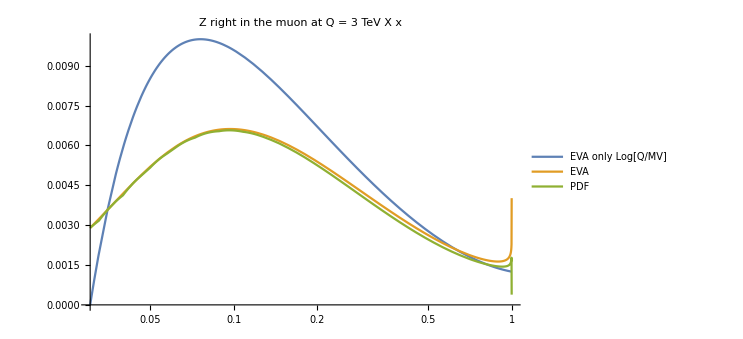

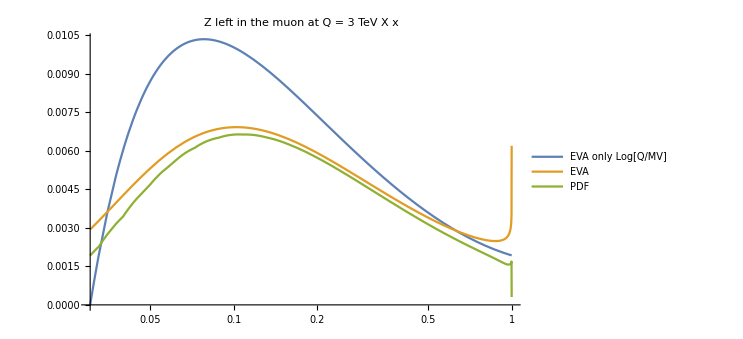

```mathematica
Q=3000

LogLogPlot[{μEVApart[Zp,Q ,x],μEVApartv2[Zp,Q ,x],μPDFpart[Zp,Q][x]},{x,(MZ/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"Z right in the muon at Q = "<>ToString[Q/1000]<>" TeV",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]
LogLogPlot[{μEVApart[Zm,Q ,x],μEVApartv2[Zm,Q ,x],μPDFpart[Zm,Q][x]},{x,(MZ/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"Z left in the muon at Q = "<>ToString[Q/1000]<>" TeV",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]
LogLogPlot[{μEVApart[ZL,Q ,x],μEVApartv2[ZL,Q ,x],μPDFpart[ZL,Q][x]},{x,(MZ/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"Z longitudinal in the muon at Q = "<>ToString[Q/1000]<>" TeV",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]


LogLinearPlot[{μEVApart[Zp,Q Sqrt[x],x],μEVApartv2[Zp,Q Sqrt[x],x],μPDFpart[Zp,Q Sqrt[x]][x]},{x,(MZ/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"Z right in the muon at Q = "<>ToString[Q/1000]<>" TeV X Sqrt[x]",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]
LogLinearPlot[{μEVApart[Zm,Q Sqrt[x],x],μEVApartv2[Zm,Q Sqrt[x],x],μPDFpart[Zm,Q Sqrt[x]][x]},{x,(MZ/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"Z left in the muon at Q = "<>ToString[Q/1000]<>" TeV X Sqrt[x]",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]
LogLinearPlot[{μEVApart[ZL,Q Sqrt[x],x],μEVApartv2[ZL,Q Sqrt[x],x],μPDFpart[ZL,Q Sqrt[x]][x]},{x,(MZ/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"Z longitudinal in the muon at Q = "<>ToString[Q/1000]<>" TeV X Sqrt[x]",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]


LogLinearPlot[{μEVApart[Zp,Q x,x],μEVApartv2[Zp,Q x,x],μPDFpart[Zp,Q x][x]},{x,(MZ/Q)^1,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"Z right in the muon at Q = "<>ToString[Q/1000]<>" TeV X x",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]
LogLinearPlot[{μEVApart[Zm,Q x,x],μEVApartv2[Zm,Q x,x],μPDFpart[Zm,Q x][x]},{x,(MZ/Q)^1,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"Z left in the muon at Q = "<>ToString[Q/1000]<>" TeV X x",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]
LogLinearPlot[{μEVApart[ZL,Q x,x],μEVApartv2[ZL,Q x,x],μPDFpart[ZL,Q x][x]},{x,(MZ/Q)^1,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"Z longitudinal in the muon at Q = "<>ToString[Q/1000]<>" TeV X x",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]
```

```mathematica
plotstyle={Thick,Thick,{Black,Dashed},{Black,DotDashed}}
```

{Thickness[Large],Thickness[Large],{GrayLevel[0],Dashing[{Small,Small}]},{GrayLevel[0],Dashing[{Small,Small}]}}

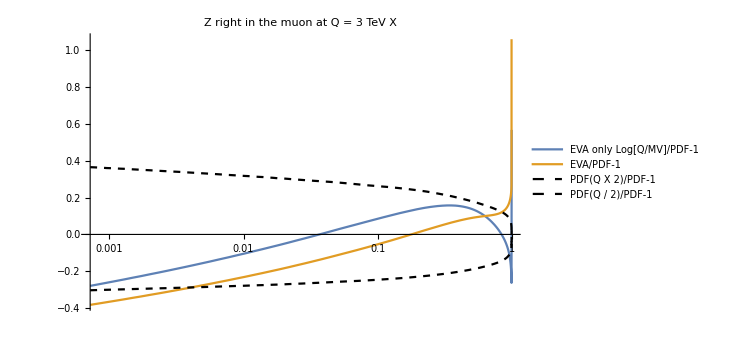

```mathematica
LogLinearPlot[{μEVApart[Zp,Q ,x]/μPDFpart[Zp,Q ][x]-1,μEVApartv2[Zp,Q ,x]/μPDFpart[Zp,Q ][x]-1,μPDFpart[Zp,Q *2][x]/μPDFpart[Zp,Q ][x]-1,μPDFpart[Zp,Q /2][x]/μPDFpart[Zp,Q ][x]-1},{x,(MW/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]/PDF-1","EVA/PDF-1","PDF(Q X 2)/PDF-1","PDF(Q / 2)/PDF-1"},PlotLabel->"Z right in the muon at Q = "<>ToString[Q/1000]<>" TeV X ",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550,PlotStyle->plotstyle]
```

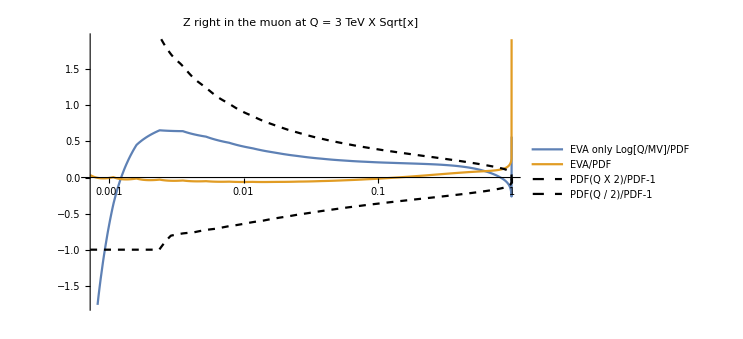

```mathematica
LogLinearPlot[{μEVApart[Zp,Q Sqrt[x],x]/μPDFpart[Zp,Q Sqrt[x]][x]-1,μEVApartv2[Zp,Q Sqrt[x],x]/μPDFpart[Zp,Q Sqrt[x]][x]-1,μPDFpart[Zp,Q Sqrt[x]*2][x]/μPDFpart[Zp,Q Sqrt[x] ][x]-1,μPDFpart[Zp,Q Sqrt[x]/2][x]/μPDFpart[Zp,Q Sqrt[x]][x]-1},{x,(MW/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]/PDF","EVA/PDF","PDF(Q X 2)/PDF-1","PDF(Q / 2)/PDF-1"},PlotLabel->"Z right in the muon at Q = "<>ToString[Q/1000]<>" TeV X Sqrt[x]",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550,PlotStyle->plotstyle]
```

```mathematica
(*DEFINIZIONE: μbPDFpart[part_,Q_][x_]:=μPDFpart[CP[part],Q][x]*)
μbEVApart[part_,Q_,x_]:=μEVApart[CP[part],Q,x]
μbEVApartv2[part_,Q_,x_]:=μEVApartv2[CP[part],Q,x]

μEVApart[ZT,Q_,x_]:=μEVApart[Zp,Q,x]+μEVApart[Zm,Q,x]
μbEVApart[ZT,Q_,x_]:=μbEVApart[Zp,Q,x]+μbEVApart[Zm,Q,x]

μEVApart[WpT,Q_,x_]:=μEVApart[Wpp,Q,x]+μEVApart[Wpm,Q,x]
μbEVApart[WpT,Q_,x_]:=μbEVApart[Wpp,Q,x]+μbEVApart[Wpm,Q,x]
μEVApart[WmT,Q_,x_]:=μEVApart[Wmp,Q,x]+μEVApart[Wmm,Q,x]
μbEVApart[WmT,Q_,x_]:=μbEVApart[Wmp,Q,x]+μbEVApart[Wmm,Q,x]


μEVApartv2[ZT,Q_,x_]:=μEVApartv2[Zp,Q,x]+μEVApartv2[Zm,Q,x]
μbEVApartv2[ZT,Q_,x_]:=μbEVApartv2[Zp,Q,x]+μbEVApartv2[Zm,Q,x]

μEVApartv2[WpT,Q_,x_]:=μEVApartv2[Wpp,Q,x]+μEVApartv2[Wpm,Q,x]
μbEVApartv2[WpT,Q_,x_]:=μbEVApartv2[Wpp,Q,x]+μbEVApartv2[Wpm,Q,x]
μEVApartv2[WmT,Q_,x_]:=μEVApartv2[Wmp,Q,x]+μEVApartv2[Wmm,Q,x]
μbEVApartv2[WmT,Q_,x_]:=μbEVApartv2[Wmp,Q,x]+μbEVApartv2[Wmm,Q,x]
```

```mathematica
listanomi={ZT,Zp,Zm,ZL,WmT,Wmp,Wpp,WmL}
listanomichiari={"Z_T","Z_R","Z_L-","Z_0","W-_T","W-_R","W-_L","W-_0"}
listaenergie={1000,3000,10000,30000}

Do[
Q=listaenergie[[k]];
Do[plotratioPDFsqrtx[i]=LogLinearPlot[{μEVApart[listanomi[[i]],Q Sqrt[x],x]/μPDFpart[listanomi[[i]],Q Sqrt[x]][x]-1,μEVApartv2[listanomi[[i]],Q Sqrt[x],x]/μPDFpart[listanomi[[i]],Q Sqrt[x]][x]-1,μPDFpart[listanomi[[i]],Q Sqrt[x]*2][x]/μPDFpart[listanomi[[i]],Q Sqrt[x] ][x]-1,μPDFpart[listanomi[[i]],Q Sqrt[x]/2][x]/μPDFpart[listanomi[[i]],Q Sqrt[x]][x]-1},{x,(MW/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]/PDF-1","EVA/PDF-1","PDF(Q X 2)/PDF-1","PDF(Q / 2)/PDF-1"},PlotLabel->listanomichiari[[i]]<>" in the muon at Q = "<>ToString[Q/1000]<>" TeV X Sqrt[x]",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550,PlotStyle->plotstyle];

Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotPDFs/ratios/"<>ToString[Q/1000]<>"TeV/"<>listanomichiari[[i]]<>"_Qsqrtx.pdf",plotratioPDFsqrtx[i] ];

plotratioPDFx[i]=LogLinearPlot[{μEVApart[listanomi[[i]],Q  x,x]/μPDFpart[listanomi[[i]],Q  x][x]-1,μEVApartv2[listanomi[[i]],Q  x,x]/μPDFpart[listanomi[[i]],Q  x][x]-1,μPDFpart[listanomi[[i]],Q  x*2][x]/μPDFpart[listanomi[[i]],Q  x ][x]-1,μPDFpart[listanomi[[i]],Q  x/2][x]/μPDFpart[listanomi[[i]],Q  x][x]-1},{x,(MW/Q),1},PlotLegends->{"EVA only Log[Q/MV]/PDF-1","EVA/PDF-1","PDF(Q X 2)/PDF-1","PDF(Q / 2)/PDF-1"},PlotLabel->listanomichiari[[i]]<>" in the muon at Q = "<>ToString[Q/1000]<>" TeV X x",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550,PlotStyle->plotstyle];

Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotPDFs/ratios/"<>ToString[Q/1000]<>"TeV/"<>listanomichiari[[i]]<>"_Qx.pdf",plotratioPDFx[i] ];

plotratioPDF[i]=LogLinearPlot[{μEVApart[listanomi[[i]],Q   ,x]/μPDFpart[listanomi[[i]],Q   ][x]-1,μEVApartv2[listanomi[[i]],Q   ,x]/μPDFpart[listanomi[[i]],Q   ][x]-1,μPDFpart[listanomi[[i]],Q   *2][x]/μPDFpart[listanomi[[i]],Q    ][x]-1,μPDFpart[listanomi[[i]],Q   /2][x]/μPDFpart[listanomi[[i]],Q   ][x]-1},{x,0.001,1},PlotLegends->{"EVA only Log[Q/MV]/PDF-1","EVA/PDF-1","PDF(Q X 2)/PDF-1","PDF(Q / 2)/PDF-1"},PlotLabel->listanomichiari[[i]]<>" in the muon at Q = "<>ToString[Q/1000]<>" TeV",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550,PlotStyle->plotstyle];

Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotPDFs/ratios/"<>ToString[Q/1000]<>"TeV/"<>listanomichiari[[i]]<>"_Q.pdf",plotratioPDF[i] ];

,{i,1, Length[listanomi]}]

,{k,1, Length[listaenergie]}
]
```

{ZT,Zp,Zm,ZL,WmT,Wmp,Wpp,WmL}

{Z_T,Z_R,Z_L-,Z_0,W-_T,W-_R,W-_L,W-_0}

{1000,3000,10000,30000}

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {26.4993} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

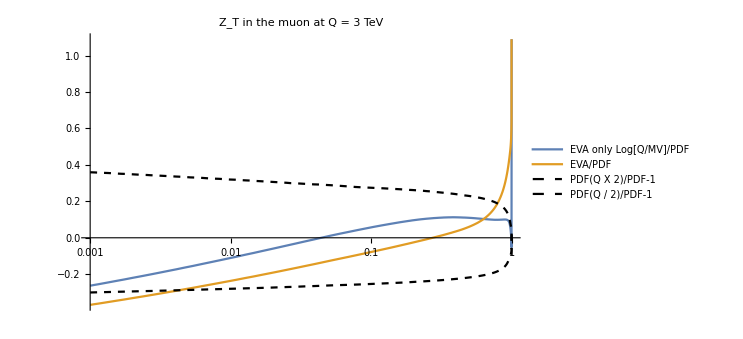

```mathematica
plotratioPDF[1]
```

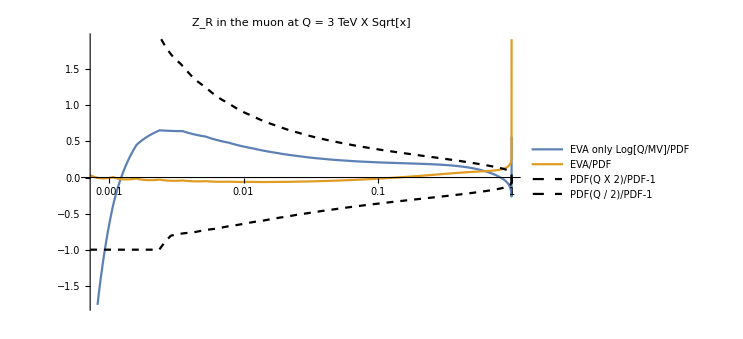

```mathematica
PLOTPTOVA[2]
```

Part::partw: Part 56 of {Z_T,Z_R,Z_L-,Z_0,W-_T,W-_R,W-_L,W-_0} does not exist.

StringJoin::string: String expected at position 1 in {Z_T,Z_R,Z_L-,Z_0,W-_T,W-_R,W-_L,W-_0}⟦56⟧<> in the muon at Q = 3 TeV X Sqrt[x].

Part::partw: Part 56 of {Z_T,Z_R,Z_L-,Z_0,W-_T,W-_R,W-_L,W-_0} does not exist.

StringJoin::string: String expected at position 1 in {Z_T,Z_R,Z_L-,Z_0,W-_T,W-_R,W-_L,W-_0}⟦56⟧<> in the muon at Q = 3 TeV X Sqrt[x].

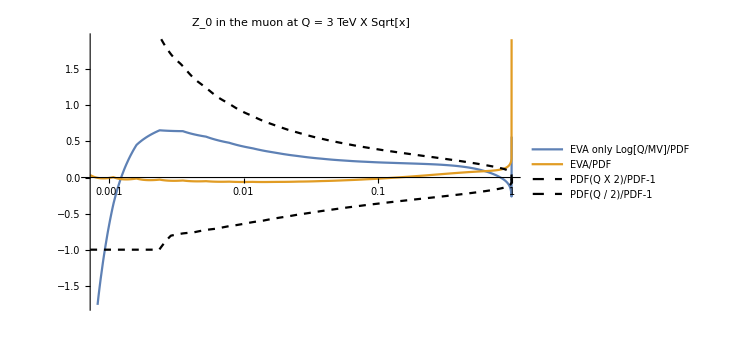

```mathematica
LogLinearPlot[{μEVApart[Zp,Q Sqrt[x],x]/μPDFpart[Zp,Q Sqrt[x]][x]-1,μEVApartv2[Zp,Q Sqrt[x],x]/μPDFpart[Zp,Q Sqrt[x]][x]-1,μPDFpart[Zp,Q Sqrt[x]*2][x]/μPDFpart[Zp,Q Sqrt[x] ][x]-1,μPDFpart[Zp,Q Sqrt[x]/2][x]/μPDFpart[Zp,Q Sqrt[x]][x]-1},{x,(MW/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]/PDF","EVA/PDF","PDF(Q X 2)/PDF-1","PDF(Q / 2)/PDF-1"},PlotLabel->listanomichiari[[i]]<>" in the muon at Q = "<>ToString[Q/1000]<>" TeV X Sqrt[x]",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550,PlotStyle->plotstyle]/.i->4
```

```mathematica
(*NEL NOTEBOOK ORIGINARIO LA SCALA era mμμ/2 nella funzione *)
```

```mathematica
(*DEFINIZIONE FUNZIONI CON mμμ e scala PDF vincolate*)
Lμmμp[part1_,part2_,mμμ_,sqrts0_]:=NIntegrate[1/x μPDFpart[part1,mμμ][x]μbPDFpart[part2,mμμ][mμμ^2/(x sqrts0^2)],{x,mμμ^2/sqrts0^2,1},AccuracyGoal->8,MaxRecursion->100]
```

```mathematica
LμmμpNpoints[part1_,part2_,mμμ_,sqrts0_,Npoints_]:=Table[{mμμ+(i-1)*(sqrts0-mμμ)/(Npoints-1),Lμmμp[part1,part2,mμμ+(i-1)*(sqrts0-mμμ)/(Npoints-1),sqrts0]},{i,1,Npoints}]
```

```mathematica
(*DEFINIZIONE FUNZIONI CON mμμ e scala PDF legate da muovermμμ*)
```

```mathematica
Lμmμpscale[part1_,part2_,mμμ_,sqrts0_,muovermμμ_]:=NIntegrate[1/x μPDFpart[part1,mμμ*muovermμμ][x]μbPDFpart[part2,mμμ*muovermμμ][mμμ^2/(x sqrts0^2)],{x,mμμ^2/sqrts0^2,1},AccuracyGoal->8,MaxRecursion->100]
```

```mathematica
LμmμpNpointsscale[part1_,part2_,mμμ_,sqrts0_,Npoints_,muovermμμ_]:=Table[{mμμ+(i-1)*(sqrts0-mμμ)/(Npoints-1),Lμmμpscale[part1,part2,mμμ+(i-1)*(sqrts0-mμμ)/(Npoints-1),sqrts0,muovermμμ]},{i,1,Npoints}]
```

```mathematica
LμmμpEVAscale[part1_,part2_,mμμ_,sqrts0_,muovermμμ_]:=NIntegrate[1/x μEVApart[part1,mμμ*muovermμμ,x]μbEVApart[part2,mμμ*muovermμμ,mμμ^2/(x sqrts0^2)],{x,mμμ^2/sqrts0^2,1},AccuracyGoal->8,MaxRecursion->100]
```

```mathematica
LμmμpEVANpointsscale[part1_,part2_,mμμ_,sqrts0_,Npoints_,muovermμμ_]:=Table[{mμμ+(i-1)*(sqrts0-mμμ)/(Npoints-1),LμmμpEVAscale[part1,part2,mμμ+(i-1)*(sqrts0-mμμ)/(Npoints-1),sqrts0,muovermμμ]},{i,1,Npoints}]
```

```mathematica
LμmμpEVAv2scale[part1_,part2_,mμμ_,sqrts0_,muovermμμ_]:=NIntegrate[1/x μEVApartv2[part1,mμμ*muovermμμ,x]μbEVApartv2[part2,mμμ*muovermμμ,mμμ^2/(x sqrts0^2)],{x,mμμ^2/sqrts0^2,1},AccuracyGoal->8,MaxRecursion->100]
```

```mathematica
LμmμpEVAv2Npointsscale[part1_,part2_,mμμ_,sqrts0_,Npoints_,muovermμμ_]:=Table[{mμμ+(i-1)*(sqrts0-mμμ)/(Npoints-1),LμmμpEVAv2scale[part1,part2,mμμ+(i-1)*(sqrts0-mμμ)/(Npoints-1),sqrts0,muovermμμ]},{i,1,Npoints}]
```

10000

0.5

2

{{200,0.0428704},{13600/19,0.00438863},{23400/19,0.0010558},{33200/19,0.000378643},{43000/19,0.00016518},{52800/19,0.0000805807},{62600/19,0.0000420714},{72400/19,0.0000228955},{82200/19,0.0000127541},{92000/19,7.17271×10^-6},{101800/19,4.02172×10^-6},{111600/19,2.22112×10^-6},{121400/19,1.1913×10^-6},{131200/19,6.09704×10^-7},{141000/19,2.90265×10^-7},{150800/19,1.23461×10^-7},{160600/19,4.35793×10^-8},{170400/19,1.08375×10^-8},{180200/19,1.1295×10^-9},{10000,0.}}

{{200,0.113905},{13600/19,0.00505241},{23400/19,0.00117642},{33200/19,0.000424151},{43000/19,0.000187176},{52800/19,0.0000924522},{62600/19,0.0000488767},{72400/19,0.0000269327},{82200/19,0.0000151923},{92000/19,8.65171×10^-6},{101800/19,4.91397×10^-6},{111600/19,2.7501×10^-6},{121400/19,1.49585×10^-6},{131200/19,7.77059×10^-7},{141000/19,3.7603×10^-7},{150800/19,1.62901×10^-7},{160600/19,5.87516×10^-8},{170400/19,1.50181×10^-8},{180200/19,1.63271×10^-9},{10000,0.}}

{{200,0.113905},{13600/19,0.00505241},{23400/19,0.00117642},{33200/19,0.000424151},{43000/19,0.000187176},{52800/19,0.0000924522},{62600/19,0.0000488767},{72400/19,0.0000269327},{82200/19,0.0000151923},{92000/19,8.65171×10^-6},{101800/19,4.91397×10^-6},{111600/19,2.7501×10^-6},{121400/19,1.49585×10^-6},{131200/19,7.77059×10^-7},{141000/19,3.7603×10^-7},{150800/19,1.62901×10^-7},{160600/19,5.87516×10^-8},{170400/19,1.50181×10^-8},{180200/19,1.63271×10^-9},{10000,0.}}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{{200,1.45697},{13600/19,-0.0487502},{23400/19,-0.0857503},{33200/19,-0.0798124},{43000/19,-0.0668338},{52800/19,-0.0526746},{62600/19,-0.0382428},{72400/19,-0.0236685},{82200/19,-0.00883053},{92000/19,0.00619744},{101800/19,0.0218573},{111600/19,0.0381609},{121400/19,0.055647},{131200/19,0.0744867},{141000/19,0.0954685},{150800/19,0.119453},{160600/19,0.148153},{170400/19,0.185756},{180200/19,0.245511},{10000,Indeterminate}}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{{200,1.45697},{13600/19,-0.0487502},{23400/19,-0.0857503},{33200/19,-0.0798124},{43000/19,-0.0668338},{52800/19,-0.0526746},{62600/19,-0.0382428},{72400/19,-0.0236685},{82200/19,-0.00883053},{92000/19,0.00619744},{101800/19,0.0218573},{111600/19,0.0381609},{121400/19,0.055647},{131200/19,0.0744867},{141000/19,0.0954685},{150800/19,0.119453},{160600/19,0.148153},{170400/19,0.185756},{180200/19,0.245511},{10000,Indeterminate}}

{WmL,WpL}

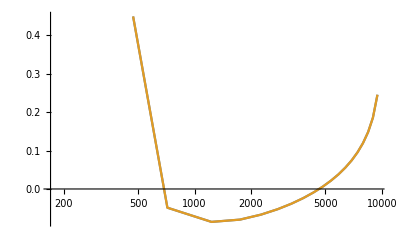

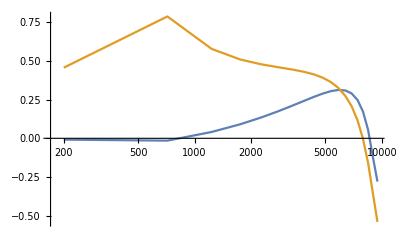

```mathematica
bins=20;
Stot=10000
minM=200;
facsc=0.5
pair=2
Tagpart1=listaluminosita[[pair,1]];
Tagpart2=listaluminosita[[pair,2]];
uno=LμmμpNpointsscale[Tagpart1,Tagpart2,minM,Stot,bins,facsc]
due=LμmμpEVAv2Npointsscale[Tagpart1,Tagpart2,minM,Stot,bins,facsc]
tre=LμmμpEVANpointsscale[Tagpart1,Tagpart2,minM,Stot,bins,facsc]
rapp1=sumconst[rapp[due,uno],-1.2]
rapp2=sumconst[rapp[tre,uno],-1.2]
listaluminosita[[pair]]
ListLogLinearPlot[{rapp1,rapp2},Joined->True]
```

```mathematica
Lμmμpscale[WmT,WpT,1000,1000,1]
```

0.

Parton luminosity for a μ- <> μ+ collider as function of the partonic  invariant mass m, which also fixes the PDF factorization scale as m/2.

```mathematica
??Do
```

```mathematica
listaluminosita[[1,2]]
```

WpT

```mathematica
listaluminosita={{WmT,WpT},{WmL,WpL},{WmL,WpT},{WmT,WpL},{ZT,ZT},{ZL,ZL},{ZL,ZT},{ZT,ZL},{Wmm,Wpm},{Wmm,Wpp},{Wmp,Wpm},{Wmp,Wpp},{Zm,Zm},{Zm,Zm},{Zp,Zm},{Zp,Zp}}
listaenergie={1000,3000,10000,30000}
```

{{WmT,WpT},{WmL,WpL},{WmL,WpT},{WmT,WpL},{ZT,ZT},{ZL,ZL},{ZL,ZT},{ZT,ZL},{Wmm,Wpm},{Wmm,Wpp},{Wmp,Wpm},{Wmp,Wpp},{Zm,Zm},{Zm,Zm},{Zp,Zm},{Zp,Zp}}

{1000,3000,10000,30000}

```mathematica
Do[

bins=20;
Stot=listaenergie[[k]];
minM=200;

Tagpart1=listaluminosita[[j,1]];
Tagpart2=listaluminosita[[j,2]];
PDFpoints=LμmμpNpointsscale[Tagpart1,Tagpart2,minM,Stot,bins,0.5];
PDFpointsscale1=LμmμpNpointsscale[Tagpart1,Tagpart2,minM,Stot,bins,1];
PDFpointsscale025=LμmμpNpointsscale[Tagpart1,Tagpart2,minM,Stot,bins,0.25];
EVApoints=LμmμpEVANpointsscale[Tagpart1,Tagpart2,minM,Stot,bins,0.5];
EVAv2points=LμmμpEVAv2Npointsscale[Tagpart1,Tagpart2,minM,Stot,bins,0.5];
EVAv2pointsscale1=LμmμpEVAv2Npointsscale[Tagpart1,Tagpart2,minM,Stot,bins,1];
EVAv2pointsscale025=LμmμpEVAv2Npointsscale[Tagpart1,Tagpart2,minM,Stot,bins,0.25];
EVApointsscale1=LμmμpEVANpointsscale[Tagpart1,Tagpart2,minM,Stot,bins,1];
EVApointsscale025=LμmμpEVANpointsscale[Tagpart1,Tagpart2,minM,Stot,bins,0.25];

plotstyle={{Thick,Black},{Thick,Blue},{Thick,Red},{Dashed,Black},{DotDashed,Black},{Dashed,Red},{DotDashed,Red},{Dashed,Blue},{DotDashed,Blue}};

Ecoll=Stot/1000;
Plot1[Tagpart1,Tagpart2]=ListLogPlot[{PDFpoints,EVApoints,EVAv2points,PDFpointsscale1,PDFpointsscale025,EVAv2pointsscale1,EVAv2pointsscale025,EVApointsscale1,EVApointsscale025},Joined->joinedoption,PlotLegends->{"PDFs (scale=m(X)/2)","EVA only Log[Q/MV] (scale=m(X)/2)","EVA (scale=m(X)/2)","PDF (scale x 2)","PDF (scale/2)","EVA (scale x 2)","EVA (scale/2)","EVA only Log[Q/MV](scale x 2)","EVA only Log[Q/MV](scale x 2)"},PlotStyle->plotstyle,BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550,Frame->True,FrameLabel->{"m(X) [GeV]","L of "<>ToString[Tagpart1]<>"-"<>ToString[Tagpart2]<>" at "<>ToString[Ecoll]<>" TeV"}];
Plot2[Tagpart1,Tagpart2]=ListPlot[{rapp[PDFpoints,PDFpoints],rapp[EVApoints,PDFpoints],rapp[EVAv2points,PDFpoints],rapp[PDFpointsscale1,PDFpoints],rapp[PDFpointsscale025,PDFpoints],rapp[EVAv2pointsscale1,PDFpoints],rapp[EVAv2pointsscale025,PDFpoints],rapp[EVApointsscale1,PDFpoints],rapp[EVApointsscale025,PDFpoints]},Joined->joinedoption,PlotLegends->{"PDFs (scale=m(X)/2)","EVA only Log[Q/MV] (scale=m(X)/2)","EVA (scale=m(X)/2)","PDF (scale x 2)","PDF (scale/2)","EVA (scale x 2)","EVA (scale/2)","EVA only Log[Q/MV](scale x 2)","EVA only Log[Q/MV](scale x 2)"},PlotStyle->plotstyle,BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550,Frame->True,FrameLabel->{"m(X) [GeV]","Ratio over L(PDFs) for "<>ToString[Tagpart1]<>"-"<>ToString[Tagpart2]<>" at "<>ToString[Ecoll]<>" TeV"}];
Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotLumi/"<>ToString[Stot/1000]<>"TeV/lumis/"<>ToString[listaluminosita[[j,1]]]<>"-"<>ToString[listaluminosita[[j,2]]]<>".pdf",Plot1[listaluminosita[[j,1]],listaluminosita[[j,2]]]];
Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotLumi/"<>ToString[Stot/1000]<>"TeV/ratios/"<>ToString[listaluminosita[[j,1]]]<>"-"<>ToString[listaluminosita[[j,2]]]<>".pdf",Plot2[listaluminosita[[j,1]],listaluminosita[[j,2]]]];
Print[{listaenergie[[k]],listaluminosita[[j,1]],listaluminosita[[j,2]]}];
,{j,1,Length[listaluminosita]},{k,1,Length[listaenergie]}
]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

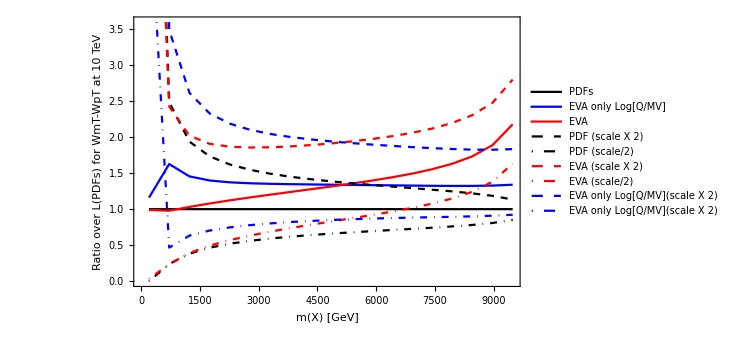
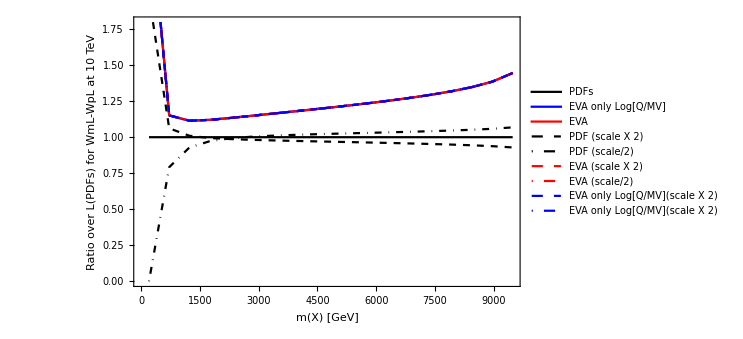
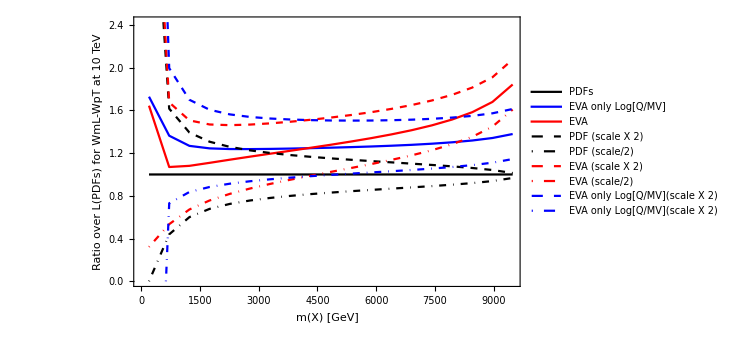
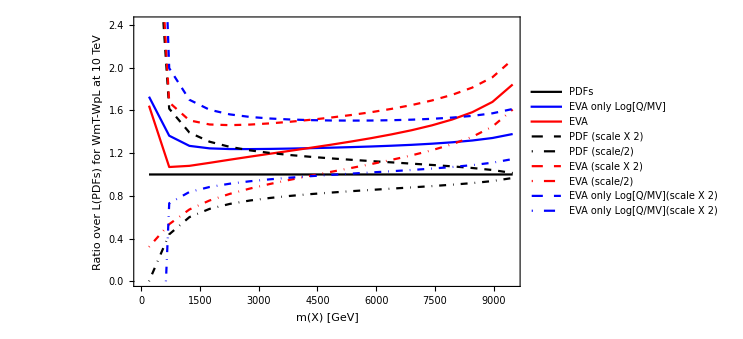

```mathematica
Table[Plot2[listaluminosita[[i,1]],listaluminosita[[i,2]]],{i,1,Length[listaluminosita]}]
```

```mathematica
(*Do[Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotLumi/"<>ToString[Stot/1000]<>"TeV/lumis/"<>ToString[listaluminosita[[i,1]]]<>"-"<>ToString[listaluminosita[[i,2]]]<>".pdf",Plot1[listaluminosita[[i,1]],listaluminosita[[i,2]]]],{i,1,Length[listaluminosita]}]
Do[Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotLumi/"<>ToString[Stot/1000]<>"TeV/ratios/"<>ToString[listaluminosita[[i,1]]]<>"-"<>ToString[listaluminosita[[i,2]]]<>".pdf",Plot1[listaluminosita[[i,1]],listaluminosita[[i,2]]]],{i,1,Length[listaluminosita]}]*)
```

```mathematica
(*

Se METTO Wp nel mu-, EVA va a zero

PDFpoints=LμmμpNpoints[WpT,WmT,minM,Stot,bins]
EVApoints=LμmμpEVANpoints[WpT,WmT,minM,Stot,bins]
EVAv2points=LμmμpEVAv2Npoints[WpT,WmT,minM,Stot,bins]

*)
```

```mathematica
joinedoption=True
```

```mathematica
True
Do[

Stot=listaenergie[[k]];

plotWmWpandWpWm=ListLogPlot[{LμmμpNpointsscale[WmT,WpT,minM,Stot,bins,0.5],LμmμpNpointsscale[WpT,WmT,minM,Stot,bins,0.5],LμmμpNpointsscale[WmL,WpL,minM,Stot,bins,0.5],LμmμpNpointsscale[WpL,WmL,minM,Stot,bins,0.5]},PlotStyle->{Black,Orange,Brown,Red,Darker[Green],Cyan,Gray,Purple,Blue,Magenta}(*,PlotRange->{{0.00099,1},{0.001,100}}*),Frame->True,FrameLabel->{"m(X) [GeV]","Luminosity"},RotateLabel->True,BaseStyle->Directive[12,FontFamily->"Times"],FrameStyle->Directive[Black],PlotLegends->{"W-_T W+_T","W+_T W-_T","W-_0 W+_0","W+_0 W-_0"},PlotLabel->"PDFs (scale=m(X)/2) Luminosity at "<>ToString[Stot/1000]<>" TeV : mu- mu+",Joined->joinedoption];
Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotLumi/"<>ToString[Stot/1000]<>"TeV/lumis/"<>"plotWmWpandWpWm.pdf",plotWmWpandWpWm];

plotWWpolTand0=ListLogPlot[{LμmμpNpointsscale[WmT,WpT,minM,Stot,bins,0.5],LμmμpNpointsscale[WmL,WpT,minM,Stot,bins,0.5],LμmμpNpointsscale[WmT,WpL,minM,Stot,bins,0.5],LμmμpNpointsscale[WmL,WpL,minM,Stot,bins,0.5]},PlotStyle->{Black,Orange,Brown,Red,Darker[Green],Cyan,Gray,Purple,Blue,Magenta}(*,PlotRange->{{0.00099,1},{0.001,100}}*),Frame->True,FrameLabel->{"m(X) [GeV]","Luminosity"},RotateLabel->True,BaseStyle->Directive[12,FontFamily->"Times"],FrameStyle->Directive[Black],PlotLegends->{"W-_T W+_T","W-_0 W+_T","W-_T W+_0","W-_0 W+_0"},PlotLabel->"PDFs (scale=m(X)/2) Luminosity at "<>ToString[Stot/1000]<>" TeV : mu- mu+",Joined->joinedoption];
Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotLumi/"<>ToString[Stot/1000]<>"TeV/lumis/"<>"plotWWpolTand0.pdf",plotWWpolTand0];

plotWWpolRandL=ListLogPlot[{LμmμpNpointsscale[WmT,WpT,minM,Stot,bins,0.5],LμmμpNpointsscale[Wmm,Wpm,minM,Stot,bins,0.5],LμmμpNpointsscale[Wmp,Wpp,minM,Stot,bins,0.5],LμmμpNpointsscale[Wmp,Wpm,minM,Stot,bins,0.5],LμmμpNpointsscale[Wmm,Wpp,minM,Stot,bins,0.5]},PlotStyle->{Black,Orange,Brown,Red,Darker[Green],Cyan,Gray,Purple,Blue,Magenta}(*,PlotRange->{{0.00099,1},{0.001,100}}*),Frame->True,FrameLabel->{"m(X) [GeV]","Luminosity"},RotateLabel->True,BaseStyle->Directive[12,FontFamily->"Times"],FrameStyle->Directive[Black],PlotLegends->{"W-_T W+_T","W-_L W+_L","W-_R W+_R","W-_R W+_L","W-_L W+_R"},PlotLabel->"PDFs (scale=m(X)/2) Luminosity at "<>ToString[Stot/1000]<>" TeV : mu- mu+",Joined->joinedoption];
Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotLumi/"<>ToString[Stot/1000]<>"TeV/lumis/"<>"plotWWpolRandL.pdf",plotWWpolRandL];

plotZZpolTand0=ListLogPlot[{LμmμpNpointsscale[ZT,ZT,minM,Stot,bins,0.5],LμmμpNpointsscale[ZL,ZT,minM,Stot,bins,0.5],LμmμpNpointsscale[ZT,ZL,minM,Stot,bins,0.5],LμmμpNpointsscale[ZL,ZL,minM,Stot,bins,0.5]},PlotStyle->{Black,Orange,Brown,Red,Darker[Green],Cyan,Gray,Purple,Blue,Magenta}(*,PlotRange->{{0.00099,1},{0.001,100}}*),Frame->True,FrameLabel->{"m(X) [GeV]","Luminosity"},RotateLabel->True,BaseStyle->Directive[12,FontFamily->"Times"],FrameStyle->Directive[Black],PlotLegends->{"Z_T Z_T","Z_0 Z_T","Z_T Z_0","Z_0 Z_0"},PlotLabel->"PDFs (scale=m(X)/2) Luminosity at "<>ToString[Stot/1000]<>" TeV : mu- mu+",Joined->joinedoption];
Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotLumi/"<>ToString[Stot/1000]<>"TeV/lumis/"<>"plotZZpolTand0.pdf",plotZZpolTand0];

plotZZpolRandL=ListLogPlot[{LμmμpNpointsscale[ZT,ZT,minM,Stot,bins,0.5],LμmμpNpointsscale[Zm,Zm,minM,Stot,bins,0.5],LμmμpNpointsscale[Zp,Zp,minM,Stot,bins,0.5],LμmμpNpointsscale[Zp,Zm,minM,Stot,bins,0.5],LμmμpNpointsscale[Zm,Zp,minM,Stot,bins,0.5]},PlotStyle->{Black,Orange,Brown,Red,Darker[Green],Cyan,Gray,Purple,Blue,Magenta}(*,PlotRange->{{0.00099,1},{0.001,100}}*),Frame->True,FrameLabel->{"m(X) [GeV]","Luminosity"},RotateLabel->True,BaseStyle->Directive[12,FontFamily->"Times"],FrameStyle->Directive[Black],PlotLegends->{"Z_T Z_T","Z_L Z_L","Z_R Z_R","Z_R Z_L","Z_L Z_R"},PlotLabel->"PDFs (scale=m(X)/2) Luminosity at "<>ToString[Stot/1000]<>" TeV : mu- mu+",Joined->joinedoption];
Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotLumi/"<>ToString[Stot/1000]<>"TeV/lumis/"<>"plotZZpolRandL.pdf",plotZZpolRandL];


plotgammaWZ=ListLogPlot[{LμmμpNpointsscale[γ,γ,minM,Stot,bins,0.5],LμmμpNpointsscale[WmT,WpT,minM,Stot,bins,0.5],LμmμpNpointsscale[WmL,WpL,minM,Stot,bins,0.5],LμmμpNpointsscale[ZT,ZT,minM,Stot,bins,0.5],LμmμpNpointsscale[ZL,ZL,minM,Stot,bins,0.5]},PlotStyle->{Black,Orange,Brown,Red,Darker[Green],Cyan,Gray,Purple,Blue,Magenta}(*,PlotRange->{{0.00099,1},{0.001,100}}*),Frame->True,FrameLabel->{"m(X) [GeV]","Luminosity"},RotateLabel->True,BaseStyle->Directive[12,FontFamily->"Times"],FrameStyle->Directive[Black],PlotLegends->{"γγ","W-_T W+_T","W-_0 W+_0","Z_T Z_T","Z_0 Z_0"},PlotLabel->"PDFs (scale=m(X)/2) Luminosity at "<>ToString[Stot/1000]<>" TeV : mu- mu+",Joined->joinedoption];
Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotLumi/"<>ToString[Stot/1000]<>"TeV/lumis/"<>"plotgammaWZ.pdf",plotgammaWZ];

,{k,1,Length[listaenergie]}]
```

True

```mathematica
(*

μbEVA has to be defined before



LμmμpEVA[part1_,part2_,mμμ_,sqrts0_]:=NIntegrate[1/x μEVApart[part1,mμμ/2][x]μbEVApart[part2,mμμ/2][mμμ^2/(x sqrts0^2)],{x,mμμ^2/sqrts0^2,1},AccuracyGoal->8,MaxRecursion->100]

LμmμpEVANpoints[part1_,part2_,mμμ_,sqrts0_,Npoints_]:=Table[{mμμ+(i-1)*(sqrts0-mμμ)/(Npoints-1),LμmμpEVA[part1,part2,mμμ+(i-1)*(sqrts0-mμμ)/(Npoints-1),sqrts0]},{i,1,Npoints}]*)
```